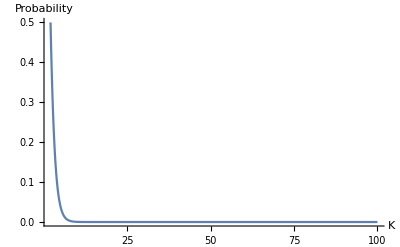

```mathematica
Plot[(k!)/k^k,{k,2,100},PlotRange->All,AxesLabel->{"K","Probability"}]
```

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
distance=1-({{1, 0.1, 0.41, 0.55, 0.35}, {0.1, 1, 0.64, 0.47, 0.98}, {0.41, 0.64, 1, 0.44, 0.85}, {0.55, 0.47, 0.44, 1, 0.76}, {0.35, 0.98, 0.85, 0.76, 1}});
```

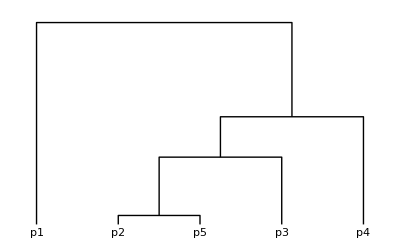

```mathematica
DendrogramPlot[DirectAgglomerate[distance,
{"p1","p2","p3","p4","p5"},Linkage->"Single"],
LeafLabels->(#&) ]
```

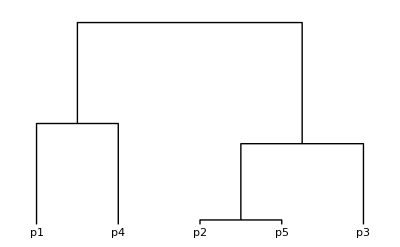

```mathematica
DendrogramPlot[DirectAgglomerate[distance,
{"p1","p2","p3","p4","p5"},Linkage->"Complete"],
LeafLabels->(#&)]
```

```mathematica
2*9^2+18
```

180

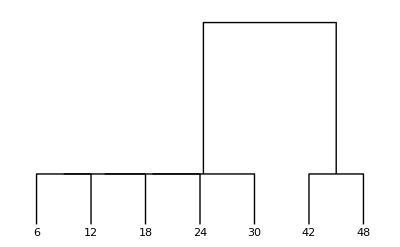

```mathematica
DendrogramPlot[Agglomerate[{6,12,18,24,30,42,48},Linkage->"Single"],LeafLabels->(#&) ]
```

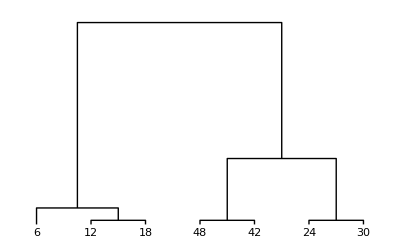

```mathematica
DendrogramPlot[Agglomerate[{6,12,18,24,30,42,48},Linkage->"Complete"],LeafLabels->(#&) ]
```

```mathematica
m=({{1, 1, 0.001, 11, 4, 676, 693}, {27, 89, 333, 827, 253, 33, 1562}, {326, 465, 8, 105, 16, 29, 949}});(* Confusion Matrix *)
p[i_,j_]:=m[[i,j]]/m[[i,7]];
e[i_]:=-Sum[N[p[i,j]*Log[2,p[i,j]]],{j,1,6}];
sum=Sum[m[[i,7]],{i,1,3}];
```

```mathematica
Table[e[i],{i,1,3}]
(* Entropy for clusters *)
```

{0.200018,1.84075,1.69641}

```mathematica
Sum[m[[i,7]]/sum*e[i],{i,1,3}]
(* Total entropy *)
```

1.44312

```mathematica
Table[N[Max[m[[i,1;;6]]]/m[[i,7]]],{i,1,3}](* Purity for clusters *)
```

{0.975469,0.529449,0.489989}

```mathematica
Sum[N[Max[m[[i,1;;6]]]/sum],{i,1,3}]
(* Total purity *)
```

0.614232